## 1.

### Demo Function

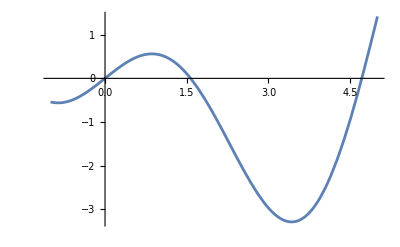

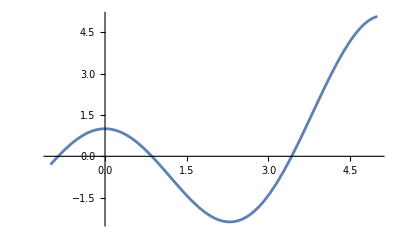

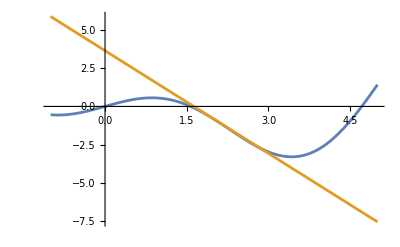

```mathematica
f[x_]:=x Cos[x];
Plot[f[x],{x,-1,5}]
Plot[f'[x],{x,-1,5}]
x0=2;
lf[x_]:=f[x0]+f'[x0]*(x-x0);
Plot[{f[x],lf[x]},{x,-1,5}]
```

### Function 1

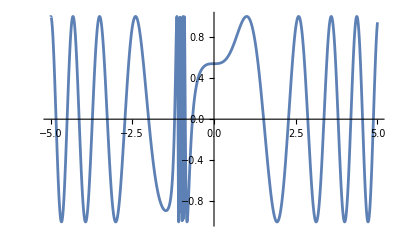

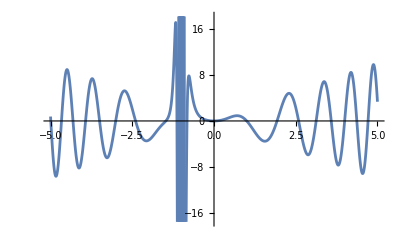

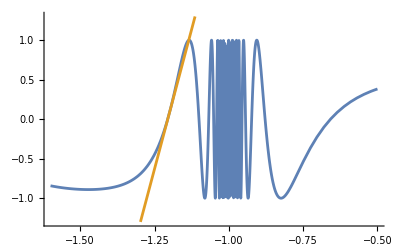

```mathematica
f1[x_] := Cos[(x^5-1)/(1+x^3)];
Plot[f1[x],{x,-5,5}]
Plot[f1'[x],{x,-5, 5}]
x0=-1.2;
lf1[x_]:=f1[x0]+f1'[x0]*(x-x0);
Plot[{f1[x],lf1[x]},{x,-1.6,-0.5}, PlotRange->{-1.3,1.3}]
```

This function has a few different points around the origin of interest for a linear approximation, but from around {x, -1.7, -0.7} there is very steep and close together oscillations that would be very difficult to approximate. As the function continues, it proceeds into normal oscillations.

### Function 2

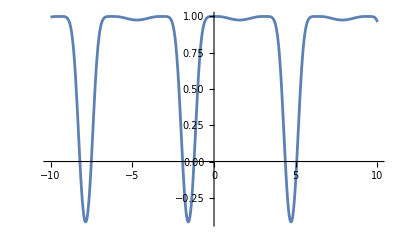

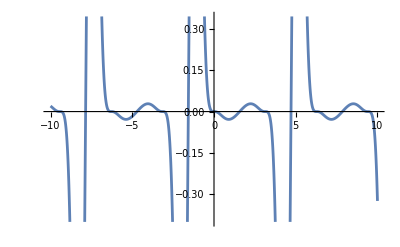

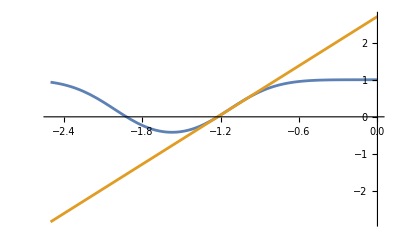

```mathematica
f2[x_]:=Cos[(1-Cos[2x])/((2+Sin[x])^2)];
Plot[f2[x],{x,-10,10}]
Plot[f2'[x],{x,-10, 10}]
x0=-1.2;
lf2[x_]:=f2[x0]+f2'[x0]*(x-x0);
Plot[{f2[x],lf2[x]},{x,-2.5,0}]
```

Certain segments of the function will be difficult to approximate because the function has large oscillations.

### Function 3

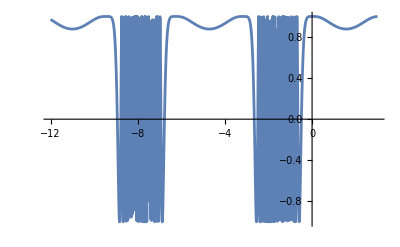

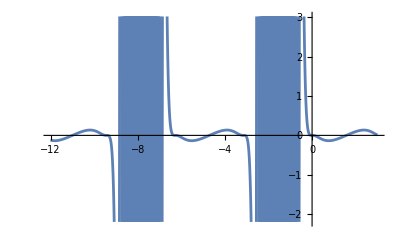

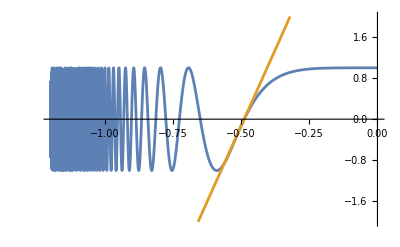

```mathematica
f3[x_]:=Cos[(1-Cos[2x])/((1+Sin[x])^2)];
Plot[f3[x],{x,-12,3}]
Plot[f3'[x],{x,-12, 3}]
x0=-0.5;
lf3[x_]:=f3[x0]+f3'[x0]*(x-x0);
Plot[{f3[x],lf3[x]},{x,-1.2,0}, PlotRange->{-2,2}]
```

Similarly to the previous function, the function has a lot of oscillation; this function has even more oscillation, with large and frequent oscillations about every 4 x-values. This makes the areas to find a linear approximation limited to the areas before or after the oscillations optimal, or in the divots between each oscillation.

### Function 4

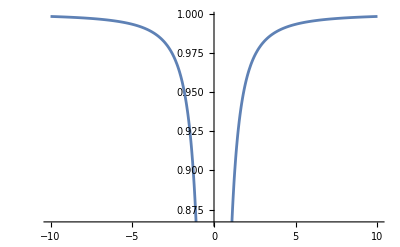

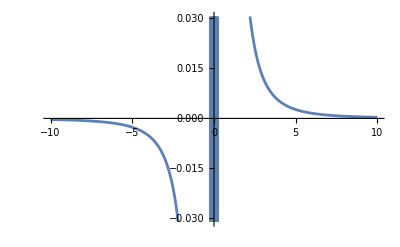

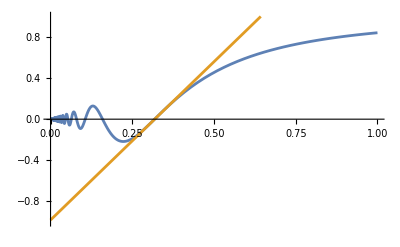

```mathematica
f4[x_]:=x*Sin[1/x];
Plot[f4[x],{x,-10,10}]
Plot[f4'[x],{x,-10, 10}]
x0=0.3;
lf4[x_]:=f4[x0]+f4'[x0]*(x-x0);
Plot[{f4[x],lf4[x]},{x,0,1}, PlotRange->{-1,1}]
```

A linear approximation for this function around -0.2 to 0.2, the oscillations get smaller and smaller and more frequent. Conversely, as the function approaches positive infinity, it flattens out, and the same for negative infinity in the opposite direction. It would be far easier to take an approximation outside of the oscillation range, as seen previously.

## 2.

```mathematica
g1[x_] :=x*Cos[x];
```

Interval

```mathematica
a = 1;
b= 5;
```

Number of approximations

```mathematica
n=7;
```

Compute the derivatives of g1 up to order n

```mathematica
taylorPoly = Normal[Series[g1[x], {x, (a + b)/2, n}]];
```

Compute the error term using the Taylor-Lagrange formula

```mathematica
errorTerm[x_] := Abs[g1[x] - taylorPoly] - (Abs[g1''[x]]*(x - a)*(x - b))/2
```

Plot the function, the Taylor polynomial, and the error term

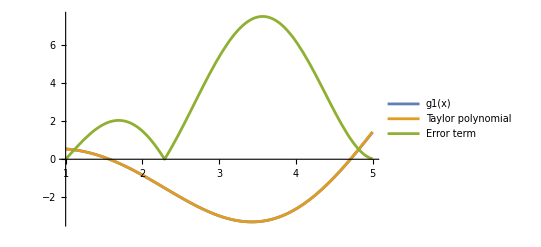

```mathematica
Plot[{g1[x], taylorPoly, errorTerm[x]}, {x, a, b}, PlotLegends -> {"g1(x)", "Taylor polynomial", "Error term"}]
```

We can see graphically that after 7 derivatives, the Taylor Expansion matches g1(x) closely. The error term shows c, and it shows were c reaches  its maximum and minimum, which happens twice over this interval.

## 3.

```mathematica
k[x_] := x^4;
a= 3;
h=20;
```

Approximation of k’(a)

```mathematica
approximation= ( k[a + h] - k[a]) /h;
```

Exact value of k’(a)

```mathematica
exact= k'[a];
```

Find the error

Taking  a  very  large  step  produces  drastic  error .

```mathematica
absoluteError = Abs[exact -approximation];
relativeError = absoluteError/Abs[exact];

approximation
exact
absoluteError
relativeError
```

13988

108

13880

3470/27

Taking a smaller step produces far less error.

```mathematica
h=0.1;
approximation= ( k[a + h] - k[a]) /h;
exact= k'[a];

absoluteError = Abs[exact -approximation];
relativeError = absoluteError/Abs[exact];

approximation
exact
absoluteError
relativeError
```

113.521

108

5.521

0.0511204

A smaller h produces less error, and a tiny h produces a negligible amount of error.

```mathematica
h=0.005;
approximation= ( k[a + h] - k[a]) /h;
exact= k'[a];

absoluteError = Abs[exact -approximation];
relativeError = absoluteError/Abs[exact];

approximation
exact
absoluteError
relativeError
```

108.27

108

0.2703

0.00250278

## 4.

Same function as question 3

With  the  improved  approximation  with  an  error  term  of  O (h^2), taking  a  larger  step  size  of  0.15  instead  of  0.005  produces  about  the  same  absolute  error  of  0.27 .

```mathematica
j[x_] := x^4
a= 3;
h = 0.15;
approximation2=( j[a + h] - j[a-h])/(2h);
exact2 = j'[a];

absoluteError2 = Abs[exact2 -approximation2];
relativeError2 = absoluteError2/Abs[exact2];

approximation2
exact2
absoluteError2
relativeError2
```

108.27

108

0.27

0.0025

And taking the same step size as the original approximation, produces a very small absolute error of 0.0003.

```mathematica
h = 0.005;

approximation2=( j[a + h] - j[a-h])/(2h);
exact2 = j'[a];

absoluteError2 = Abs[exact2 -approximation2];
relativeError2 = absoluteError2/Abs[exact2];

approximation2
exact2
absoluteError2
relativeError2
```

108.

108

0.0003

2.77778×10^-6